```mathematica
FormulaGraphReverse2[allGraphs4[K4Key,"colofourrealnull"]]
```

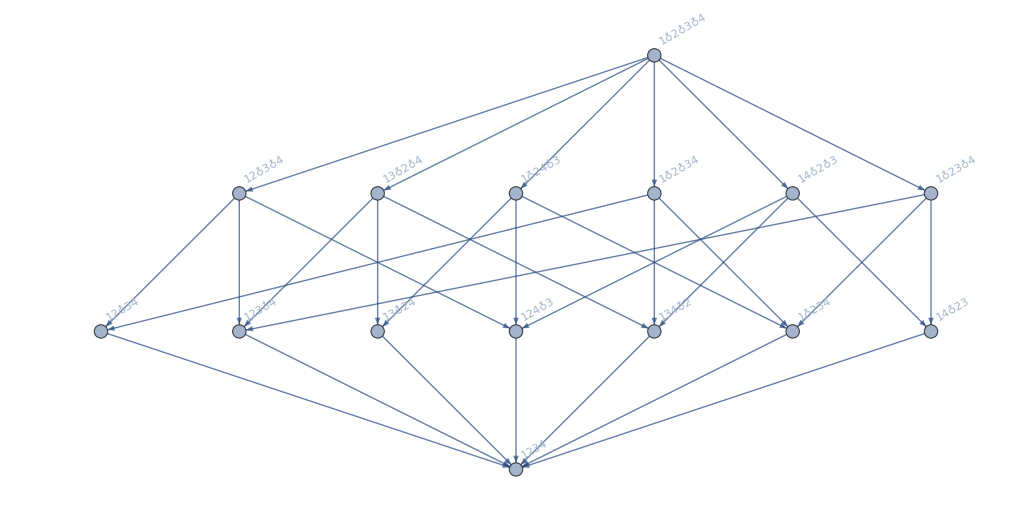

```mathematica
MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[allGraphs4[K4Key,"colofourrealnull"]],CompareSymbols]]]//MatrixForm
```

(1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 2 | 1 | 2 | 1 | 1 | 2 | -6
0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 2
0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 2
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

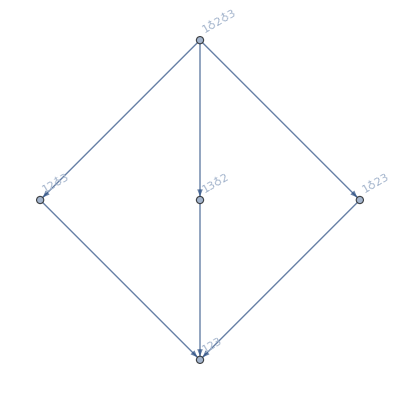

```mathematica
FormulaGraphReverse2[allGraphs3[K3Key,"colofourrealnull"]]
```

```mathematica
MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[allGraphs3[K3Key,"colofourrealnull"]],CompareSymbols]]]//MatrixForm
```

(1 | -1 | -1 | -1 | 2
0 | 1 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1)

```mathematica
Table[allGraphs3[k,"colofourrealnull"],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3,n12x3,n123,n13x2,n1x23}

```mathematica
Keys[allGraphs3]//Length
```

15

```mathematica
Table[Labeled[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[allGraphs3[k,"colofourrealnull"]],CompareSymbols]]]//MatrixForm,allGraphs3[k,"graph"]],{k,Keys[allGraphs3]}]
```

{(1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1 | -1 | 2
0 | 1 | 0 | -1
0 | 0 | 1 | -1
0 | 0 | 0 | 1)-Graphics-,(1 | -1 | -1 | -1 | 2
0 | 1 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1 | -1 | 2
0 | 1 | 0 | -1
0 | 0 | 1 | -1
0 | 0 | 0 | 1)-Graphics-,(1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1 | -1 | 2
0 | 1 | 0 | -1
0 | 0 | 1 | -1
0 | 0 | 0 | 1)-Graphics-,(1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1)-Graphics-}

```mathematica
Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]
```

{0,9,12,13,10,3,4,1}

```mathematica
Table[allGraphs3[k,"graph"],{k,Select[Keys[allGraphs3],VertexCount[allGraphs3[#,"graph"]]==3&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Labeled[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[allGraphs3[k,"colofourrealnull"]],CompareSymbols]]]//MatrixForm,allGraphs3[k,"graph"]],{k,Select[Keys[allGraphs3],EdgeCount[allGraphs3[#,"graph"]]==1&]}]
```

{(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-,(1 | -1
0 | 1)-Graphics-}

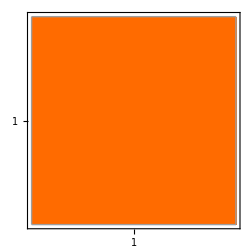
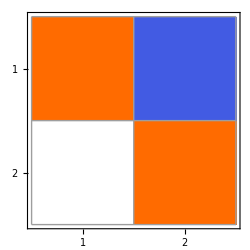
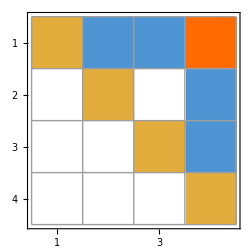
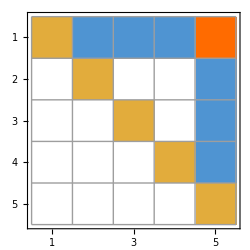
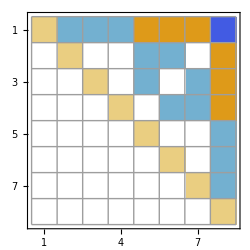
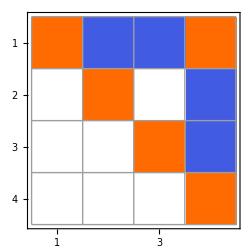
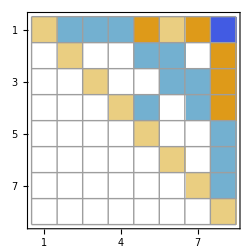
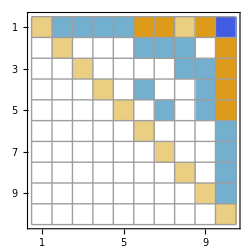
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
With[
{sets=allGraphs4},
Table[Labeled[MatrixPlot[MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[k,"colofourrealnull"]],CompareSymbols]]],Mesh->All, ImageSize->250],sets[k,"graph"]],{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==4&]]}]
]
```

```mathematica
With[
{sets=allGraphs5},
Map[Last,
Sort[Table[With[{mat=MobiusMatrixFromSets[Map[SymbolToSets,Sort[ListofVars[sets[k,"colofourrealnull"]],CompareSymbols]]]},
{Length[mat],Labeled[MatrixPlot[mat,Mesh->All, ImageSize->250],sets[k,"graph"]]}],{k,Sort[Select[Keys[sets],VertexCount[sets[#,"graph"]]==5&]]}]]
]
]
```